Automated Theorem Proving for Equational Logic

Gorard Jonathan

Barbieri Carlo

Department of Mathematics, King’s College London

Most representative image

-Graphics--Graphics-

Abstract

GOAL OF THE PROJECT: To extend the backend of Mathematica’s FullSimplify function, in an effort to construct a system for automatically generating and visualizing proofs of arbitrary theorems in first-order equational logic.

SUMMARY OF WORK: I began by generalizing the pre-existing Knuth-Bendix unfailing completion algorithm, thereby constructing a more sophisticated algorithm that would be able to auto-generate abstract proof networks of arbitrary theorems, not only in first-order equational logic, but in any finite axiom system based on first-order equational logic. I subsequently experimented with methods for automatically presenting such proofs in human natural language, using various heuristics to determine the appropriate conceptual waypoints for guiding the reader through the logic of the proof. Finally, I implemented an automatic proof-verification algorithm, which is able to convert any such proof into executable Mathematica code.

RESULTS AND FUTURE  WORK: With the framework for automatic proof-generation, proof-presentation and proof-verification already implemented, the obvious next step would be to add functionality for exporting proofs in such a format that they could be uploaded directly to the Wolfram Data Repository. In addition, with further backend development, these tools could be used to gain deeper insight into certain longstanding results, such as the proof of correctness of the Wolfram axiom for Boolean algebra.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

Automatically proving theorems from arbitrary axiom systems: 

-Graphics-

-Graphics--Graphics--Graphics-

Auto-generating human-readable LATEX papers:

-Graphics--Graphics-

Automatic proof-verification:

-Graphics-

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Basic Results

Let’s start by proving an elementary theorem from a single axiom.

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"project.m"}]]
```

```mathematica
addAxiom[ForAll[{x,y},f[x,y]==f[y,x]]]
```

∀_{x,y}f[x,y]==f[y,x]

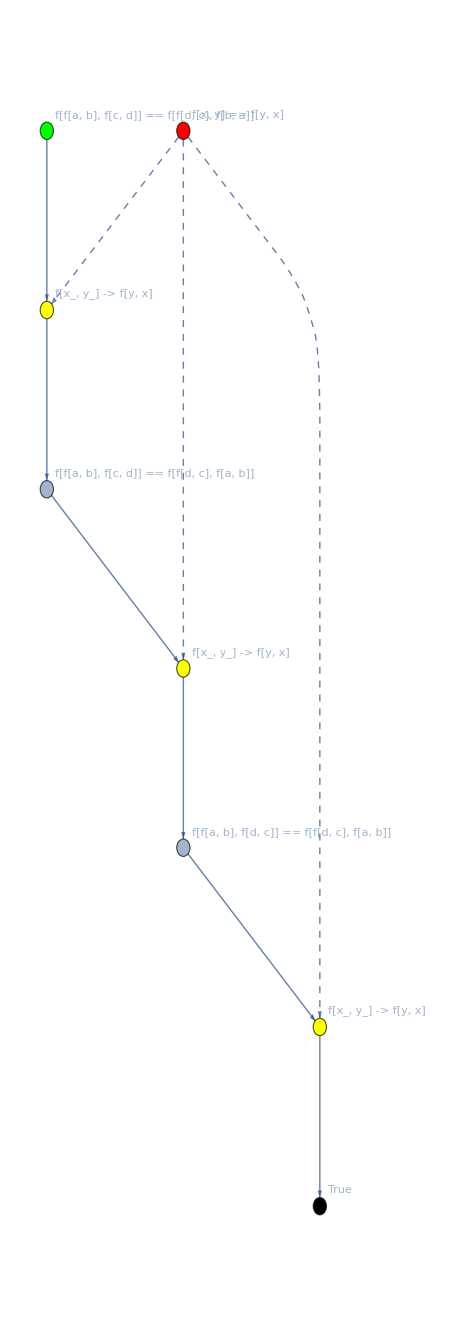

```mathematica
proveTheorem[ForAll[{a,b,c,d},f[f[a,b],f[c,d]]==f[f[d,c],f[b,a]]]]
```

All proof networks are based on this essential structure: starting from the axioms (coloured in red), one applies a sequence of syntactic transformations (coloured in yellow), justified either by the axioms or by intermediate lemmas (with the justifications represented by dashed lines), in order to ultimately deduce that the theorem (coloured in green) is true. Let’s now prove some more nontrivial theorems, taken from the NKS book, regarding various algebraic properties of the NAND operator in Boolean algebra:

```mathematica
clearAxioms[]
```

True

```mathematica
addAxiom[ForAll[{a,b},f[f[a,a],f[a,b]]==a]]
```

∀_{a,b}f[f[a,a],f[a,b]]==a

```mathematica
addAxiom[ForAll[{c,d},f[c,f[c,d]]==f[c,f[d,d]]]]
```

∀_{c,d}f[c,f[c,d]]==f[c,f[d,d]]&&∀_{a,b}f[f[a,a],f[a,b]]==a

```mathematica
addAxiom[ForAll[{x,y,z},f[x,f[x,f[y,z]]]==f[y,f[y,f[x,z]]]]]
```

∀_{x,y,z}f[x,f[x,f[y,z]]]==f[y,f[y,f[x,z]]]&&∀_{c,d}f[c,f[c,d]]==f[c,f[d,d]]&&∀_{a,b}f[f[a,a],f[a,b]]==a

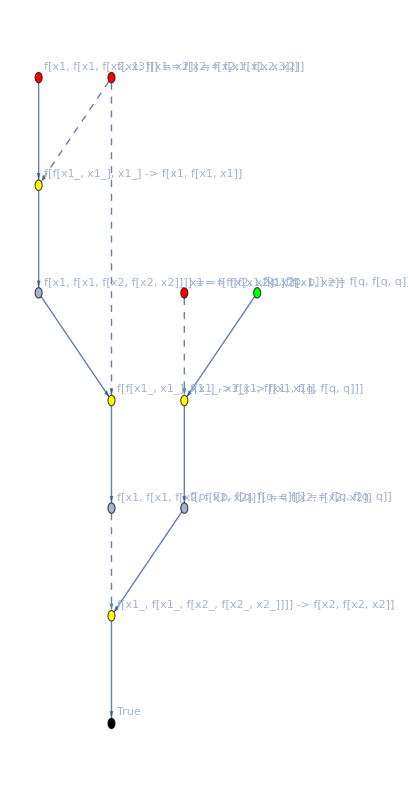

```mathematica
proveTheorem[ForAll[{p,q},f[p,f[p,p]]==f[q,f[q,q]]]]
```

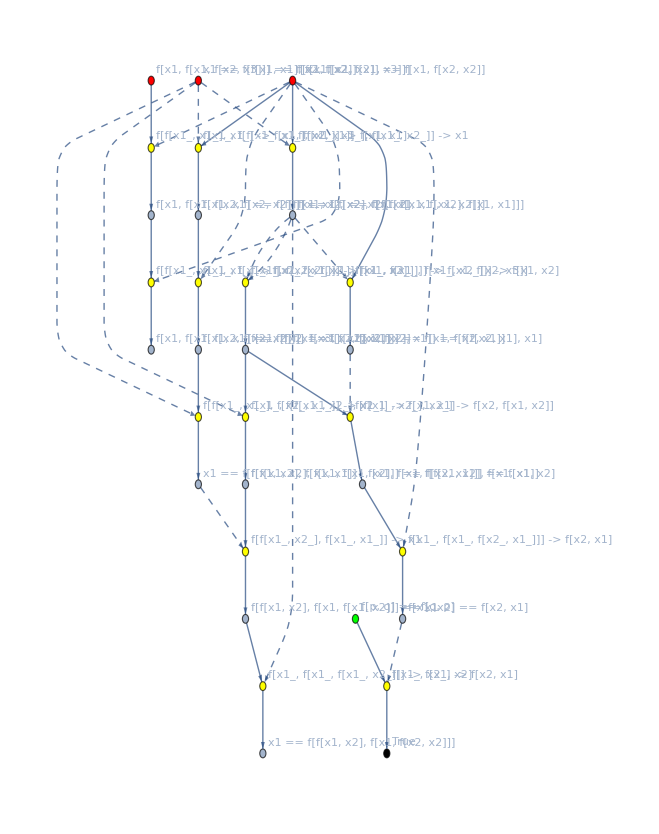

```mathematica
proveTheorem[ForAll[{p,q},f[p,q]==f[q,p]]]
```

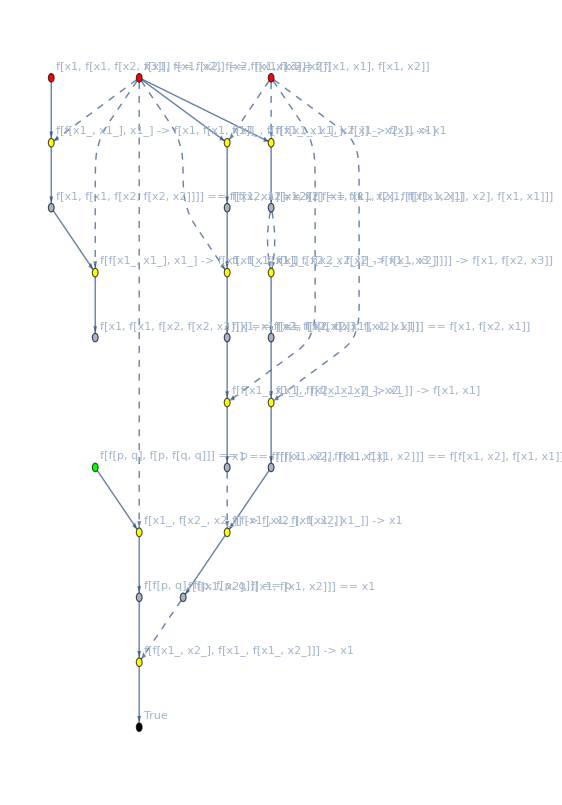

```mathematica
proveTheorem[ForAll[{p,q},p==f[f[p,q],f[p,f[q,q]]]]]
```

Internally, the theorem-proving system is based on the Knuth-Bendix unfailing completion algorithm for equational logic, which begins by considering the abstract proof tree of all possible axiomatic transformations (such that, if the theorem is true, then its proof will correspond to at least one branch of the tree). The algorithm then uses a combination of rule orientation and critical pairing to construct a confluent term-rewriting system, and determine which branches of the tree to actually traverse.

Code

https://github.com/GetJonWithIt/starthere

Written Content / Lesson Plans

Further Results and Analysis

In the case of more nontrivial proofs, abstract proof networks are not particularly easy for humans to read or understand, so I began experimenting with alternative methods for presenting such proofs in a more human-readable way. One of the fundamental challenges in making machine-generated proofs human-comprehensible is that they lack the kind of conceptual waypoints that guide the reader through the logic of a conventional mathematical proof (published proofs tend to “tell a story” of how a particular result was derived, rather than simply presenting an abstract sequence of logical transformations).

As a preliminary heuristic for automatically finding conceptual waypoints for a given proof, I tried searching for nodes in the proof network with a higher-than-average connection density (since the associated lemmas will, by definition, represent the “load-bearing pieces” in the logical structure of the proof). When presenting the proof to a human reader, such lemmas are introduced first (in order to give the reader an intuitive picture of the large-scale formal structure of the argument), and then the remaining details are filled in, in a recursive/hierarchical fashion.

```mathematica
clearAxioms[]
```

True

```mathematica
addAxiom[ForAll[{x,y},f[x,y]==f[y,x]]]
```

∀_{x,y}f[x,y]==f[y,x]

```mathematica
presentProof[ForAll[{a,b,c,d},f[f[a,b],f[c,d]]==f[f[d,c],f[b,a]]]]
```

proof.tex

The presentProof function outputs a TEX file, which (when compiled) produces an auto-generated mathematics paper, presenting the proof in a style which I think is reasonably similar to how a human mathematician might write it.

Since all proofs are represented internally as sequences of syntactic transformations, this makes them immediately amenable to the techniques of automated proof checking. With this in mind, I added the function checkProof, which takes a given proof and automatically converts it to a blob of Mathematica code. The code represents the theorem and the axioms as symbolic expressions, and then uses MapAt, Replace and ReplaceAll to apply the requisite syntactic transformations in the correct places, and deduce that the theorem is, indeed, true.

```mathematica
checkProof[ForAll[{a,b,c,d},f[f[a,b],f[c,d]]==f[f[d,c],f[b,a]]]]
```

```mathematica
Hold[s1=f[x,y]==f[y,x];s2=f[f[a,b],f[c,d]]==f[f[d,c],f[b,a]];s4=MapAt[Replace[f[x_,y_]->f[y,x]],s2,{2,2}];s5=MapAt[Replace[f[x_,y_]->f[y,x]],s4,{1,2}];s6=MapAt[ReplaceAll[f[x_,y_]->f[y,x]],s5,2]]
```

Hold[s1=f[x,y]==f[y,x];s2=f[f[a,b],f[c,d]]==f[f[d,c],f[b,a]];s4=MapAt[Replace[f[x_,y_]→f[y,x]],s2,{2,2}];s5=MapAt[Replace[f[x_,y_]→f[y,x]],s4,{1,2}];s6=MapAt[ReplaceAll[f[x_,y_]→f[y,x]],s5,2]]

```mathematica
ReleaseHold[%]
```

True

Thus, since every auto-generated proof can be programmatically represented as a piece of symbolic Mathematica code in this way, it becomes possible to do something which cannot conventionally be done with a human-written proof: in addition to simply reading it, one can also actually run it.

All Visualizations

A sample PDF file output by presentProof:

```mathematica
-Graphics-
-Graphics-
```

Data Sources Links/References

Future Directions

Background Info Links/References

http://mathworld.wolfram.com/Knuth-BendixCompletionAlgorithm.html
http://www.cs.miami.edu/home/geoff/Courses/TPTPSYS/FirstOrder/Paramodulation.shtml
http://mathworld.wolfram.com/CriticalPair.html
http://mathworld.wolfram.com/Confluence.html

Keywords

Mathematics

Automated Theorem Proving

Other

Date

Last Modified: Tuesday, July 04, 2017

```mathematica
"Add Timestamp"
```